```mathematica
SteadyState[R_] := Module[{ps},
	ps = Table[(-1)^i Det[Drop[R,{2},{i}]], {i,Length@R}];
	ps /= Total[ps];
	ps
]
RootedTree[tree_, root_] := Module[{A2,treeadj,target,layer,layernew,d},
	d = Length[tree] + 1;
	A2 = Table[0, {i,d}, {j,d}];
	treeadj = ReplacePart[A2, Flatten[{{#1,#2}->1,{#2,#1}->1} &@@@ tree]];
	target = Table[If[i==root,0,1],{i,d}];
	layer = {root}; layernew={root};
	Do[
		If[Total[treeadj,{2}] == target, Break[];];
		Do[If[(¬MemberQ[layer,i]), treeadj[[#,i]]=0], {i,d}] &/@ layernew;
		layer = layernew;
		layernew = Flatten[Position[treeadj[[;;,#]],1] &/@ layer];
	,{rep,d}];
	EdgeList @ AdjacencyGraph @ treeadj
]

Deletion[trees_, edge_] := Module[{},
	DeleteCases[trees, _?(MemberQ[#, edge[[1]] -> edge[[2]]]&)]
]

Contraction[trees_,edge_] := Module[{res},
	res = DeleteCases[trees, _?(Not[MemberQ[#, edge[[1]] -> edge[[2]]]]&)];
	DeleteElements[#, {edge[[1]] -> edge[[2]]}] &/@ res
]
```

## Tutorial

This is a tutorial to illustrate the results in arXiv:2402.13193 and aid their applications.

### Functions and main ideas

In this tutorial, we start with a rate matrix defining the continuous-time Markov chain, it can have numerical and/or symbolic entries. We warn you that if the network is too large, the number of spanning trees will be huge. 
Evaluate cell by cell.

We start with the rate matrix of the Myosin-V model, used in the Appendix of the paper.

```mathematica
R={{0,r12,0,0,r15,0},{r21,0,r23,0,0,r26},{0,r32,0,r34,0,0},{0,0,r43,0,r45,r46},{r51,0,0,r54,0,0},{0,r62,0,r64,0,0}};
```

Now we get the adjacency matrix and its undirected graph:

```mathematica
A=(R+Transpose[R])//ArrayComponents//Unitize;
A//MatrixForm
g=AdjacencyGraph[A,EdgeStyle->Black,VertexStyle->White,ImageSize->100,VertexLabels->"Name",VertexCoordinates->{1->{0,1.7},2->{1.6,0.5},3->{1,-1.4},4->{-1,-1.4},5->{-1.6,0.5},6->{0,0.5}}]
```

(0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0)

-Graphics-

Spanning trees:

```mathematica
d=Length@A;
trees=Select[TreeGraphQ[Graph@#]&]@Select[VertexCount@#==d&]@Subsets[EdgeList[g],{d-1}];
Multicolumn[HighlightGraph[g,#,GraphHighlightStyle->"Thick"] &/@ trees,4]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

We will only deal with rooted spanning-trees, that’s how you root them:

```mathematica
root=1;
rootedtrees = RootedTree[#,root] &/@ trees;
Multicolumn[HighlightGraph[DirectedGraph@g,#,GraphHighlightStyle->"Thick"] &/@ rootedtrees,4]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

This is what happens when you delete an edge, i.e. remove all spanning trees containing this edge:

```mathematica
edge={2,1}; (*notice that the order matters*)
Multicolumn[HighlightGraph[DirectedGraph@g,#,GraphHighlightStyle->"Thick"]&/@Deletion[rootedtrees,edge],4]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

This is what happens when you contract an edge, i . e . only keep spanning trees containing this edge and then remove it:

```mathematica
Multicolumn[HighlightGraph[DirectedGraph@g,#,GraphHighlightStyle->"Thick"]&/@Contraction[rootedtrees,edge],4]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

### Susceptibility from spanning trees

For convenience, we will make a function out of the process of getting spanning trees from the rate matrix:

```mathematica
TreesFromRateMatrix[R_] := Module[{A,d,g},
	A = (R+Transpose[R]) // ArrayComponents // Unitize;
	d = Length @ A;
	g = AdjacencyGraph[A];
	Select[TreeGraphQ[Graph@#]&] @ Select[VertexCount@#==d&] @ Subsets[EdgeList[g], {d-1}]
]
```

For the mutual linearity of nonequilibrium currents, we define an input and an output edge:

```mathematica
R={{0,r12,0,0,r15,0},{r21,0,r23,0,0,r26},{0,r32,0,r34,0,0},{0,0,r43,0,r45,r46},{r51,0,0,r54,0,0},{0,r62,0,r64,0,0}};
input={3,4};
output={5,1}; (*This is expressed as "e" in the paper*)
```

For Eq . (5) of ,  we have to modify the original graph. First we remove input and output, then add and contract an edge (connection operation)

```mathematica
R[[input[[2]],input[[1]]]]=0;R[[input[[1]],input[[2]]]]=0;
R[[output[[2]],output[[1]]]]=0;R[[output[[1]],output[[2]]]]=0;
connection={output[[1]],input[[1]]};
R[[connection[[1]],connection[[2]]]]+=1;
```

Let’s see some rooted spanning trees

```mathematica
trees=TreesFromRateMatrix[R];
root=1;
rootedtrees = RootedTree[#,root] &/@ trees;
A=(R+Transpose[R])//ArrayComponents//Unitize;
g=AdjacencyGraph[A,EdgeStyle->Black,VertexStyle->White,ImageSize->100,VertexLabels->"Name",VertexCoordinates->{1->{0,1.7},2->{1.6,0.5},3->{1,-1.4},4->{-1,-1.4},5->{-1.6,0.5},6->{0,0.5}}];
Multicolumn[HighlightGraph[DirectedGraph@g,#,GraphHighlightStyle->"Thick"]&/@Contraction[rootedtrees,connection],4]
```

-Graphics- | -Graphics- | -Graphics- |

The value of tau:

```mathematica
Sum[ (Times @@ (R[[#2,#1]] &@@@ ({#[[1]],#[[2]]} &/@ rt))) , {rt, Contraction[rootedtrees,connection]}]
```

r12 r23 r26 r54+r12 r23 r46 r54+r12 r23 r26 r64

Finally, let’s automate the process and compute the susceptibility

```mathematica
Tau[R_][dels_, cons_] := Module[{d,trees,rootedtrees,sum},
	d = Length[R];
	trees = TreesFromRateMatrix[R];
	sum = 0;
	Do[
		rootedtrees = RootedTree[#,root] &/@ trees;
		rootedtrees = Fold[Deletion, rootedtrees, dels];
		rootedtrees = Fold[Contraction, rootedtrees, cons];
		sum += Total @ Table[ (Times @@ (R[[#2,#1]] &@@@ ({#[[1]],#[[2]]} &/@ rt))) , {rt, rootedtrees}];
	,{root, d}];
	sum	
]
Susceptibility[R_, input_, output_] := Module[{R2,tau1,tau2,tau3,tau4,tauden,dels},
	R2 = R; R2[[input[[1]],output[[1]]]] = 1;
	dels = {input, Reverse@input, output, Reverse@output};
	tau1 = Tau[R2][dels, {{output[[1]],input[[1]]}}];
	R2 = R; R2[[input[[2]],output[[1]]]] = 1;
	tau2 = Tau[R2][dels, {{output[[1]],input[[2]]}}];
	R2 = R; R2[[input[[1]],output[[2]]]] = 1;
	tau3 = Tau[R2][dels, {{output[[2]],input[[1]]}}];
	R2 = R; R2[[input[[2]],output[[2]]]] = 1;
	tau4 = Tau[R2][dels, {{output[[2]],input[[2]]}}];
	tauden = Tau[R][{input,Reverse@input},{}];
	1/tauden( R[[output[[2]],output[[1]]]](tau1-tau2) - R[[output[[1]],output[[2]]]](tau3-tau4))
]
```

```mathematica
values={r21->10^5,r12->0.49,r32->4.6 10^3,r23->6.4 10^4,r43->3 10^3,r34->P 4.64,r54->15.2,r45->3.35,r15->302.8,r51->0.62,r64->6.9 10^-2,r46->1.5 10^-2,r26->302.8,r62->1.27 10^-6 };
R={{0,r12,0,0,r15,0},{r21,0,r23,0,0,r26},{0,r32,0,r34,0,0},{0,0,r43,0,r45,r46},{r51,0,0,r54,0,0},{0,r62,0,r64,0,0}};
λ1=Susceptibility[R,input, output]
λ1/.values
```

(r15 (r12 r23 r26 r54+r21 r23 r26 r54+r21 r26 r32 r54+r12 r23 r46 r54+r21 r23 r46 r54+r21 r32 r46 r54+r21 r23 r54 r62+r21 r46 r54 r62)-r51 (-r12 r23 r26 r45-r12 r23 r45 r46-r12 r23 r26 r54-r12 r23 r46 r54-r12 r23 r45 r64+r12 r26 r45 r64))/(r12 r23 r26 r45 r51+r12 r23 r45 r46 r51+r12 r15 r23 r26 r54+r15 r21 r23 r26 r54+r15 r21 r26 r32 r54+r12 r15 r23 r46 r54+r15 r21 r23 r46 r54+r15 r21 r32 r46 r54+r12 r23 r26 r51 r54+r12 r23 r46 r51 r54+r15 r21 r23 r46 r62+r21 r23 r45 r46 r62+r23 r45 r46 r51 r62+r15 r21 r23 r54 r62+r15 r23 r46 r54 r62+r21 r23 r46 r54 r62+r23 r46 r51 r54 r62+r12 r15 r23 r26 r64+r15 r21 r23 r26 r64+r15 r21 r26 r32 r64+r12 r23 r26 r45 r64+r21 r23 r26 r45 r64+r21 r26 r32 r45 r64+r12 r23 r26 r51 r64+r12 r23 r45 r51 r64+r23 r26 r45 r51 r64+r26 r32 r45 r51 r64+r15 r21 r23 r62 r64+r21 r23 r45 r62 r64+r23 r45 r51 r62 r64)

0.995431

We also visualize which spanning trees go into each τ of the susceptibility expression. For a given connection 5->4, here are the trees whose polynomials will go into (τ^(/5->4))_(\{(5-1),Pi})

```mathematica
connection={5,4};
R2 = R; R2[[connection[[2]],connection[[1]]]] = 1;
Tau[R2][{input,Reverse@input,output,Reverse@output},{connection}] 
A=(R2+Transpose[R2])//ArrayComponents//Unitize;
g=AdjacencyGraph[A,EdgeStyle->Black,VertexStyle->White,ImageSize->100,VertexLabels->"Name",VertexCoordinates->{1->{0,1.7},2->{1.6,0.5},3->{1,-1.4},4->{-1,-1.4},5->{-1.6,0.5},6->{0,0.5}}];
dels={input,Reverse@input,output,Reverse@output};cons={connection};
vec={};Do[
trees = TreesFromRateMatrix[R2];
rootedtrees = RootedTree[#,root] &/@ trees;
rootedtrees = Fold[Deletion, rootedtrees, dels];
rootedtrees = Fold[Contraction, rootedtrees, cons];
AppendTo[vec,HighlightGraph[DirectedGraph@g,#,GraphHighlightStyle->"Thick"]&/@rootedtrees];
,{root,d}]
Multicolumn[Flatten@vec,5]
```

r21 r23 r46 r62+r12 r23 r26 r64+r21 r23 r26 r64+r21 r26 r32 r64+r21 r23 r62 r64

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Hands-on

Lastly, just input any rate matrix without the diagonal elements below, choose an input and output edge, and the program will provide the affine coefficient and the susceptibility.

```mathematica
R={{0,r12,r13,0},{r21,0,r23,r24},{r31,r32,0,r34},{r41,r42,r43,0}};
input={1,2};output={4,3};
Rstall=R;Rstall[[input[[2]],input[[1]]]]=0;Rstall[[input[[1]],input[[2]]]]=0;
pssstall=SteadyState[Rstall-DiagonalMatrix[Total[Rstall]]];
λ0=pssstall[[output[[1]]]]R[[output[[2]],output[[1]]]]-pssstall[[output[[2]]]]R[[output[[1]],output[[2]]]]
λ1=Susceptibility[R,input, output]
```

-(((-r24 r31 r32-r31 r32 r34-r24 r32 r41-r32 r34 r41-r31 r34 r42-r34 r41 r42) r43)/(-r23 r24 r31-r13 r24 r32-r24 r31 r32-r23 r31 r34-r13 r32 r34-r31 r32 r34-r13 r24 r41-r23 r24 r41-r13 r32 r41-r24 r32 r41-r23 r34 r41-r32 r34 r41-r23 r31 r42-r13 r34 r42-r31 r34 r42-r13 r41 r42-r23 r41 r42-r34 r41 r42-r24 r31 r43-r31 r32 r43-r24 r41 r43-r32 r41 r43-r31 r42 r43-r41 r42 r43))+(r34 (-r13 r32 r41-r23 r31 r42-r13 r41 r42-r23 r41 r42-r31 r32 r43-r32 r41 r43-r31 r42 r43-r41 r42 r43))/(-r23 r24 r31-r13 r24 r32-r24 r31 r32-r23 r31 r34-r13 r32 r34-r31 r32 r34-r13 r24 r41-r23 r24 r41-r13 r32 r41-r24 r32 r41-r23 r34 r41-r32 r34 r41-r23 r31 r42-r13 r34 r42-r31 r34 r42-r13 r41 r42-r23 r41 r42-r34 r41 r42-r24 r31 r43-r31 r32 r43-r24 r41 r43-r32 r41 r43-r31 r42 r43-r41 r42 r43)

(r34 (-r13 r41-r23 r41-r32 r41+r13 r42+r23 r42+r31 r42)-(-r24 r31+r24 r32+r32 r41-r31 r42) r43)/(r23 r24 r31+r13 r24 r32+r24 r31 r32+r23 r31 r34+r13 r32 r34+r31 r32 r34+r13 r24 r41+r23 r24 r41+r13 r32 r41+r24 r32 r41+r23 r34 r41+r32 r34 r41+r23 r31 r42+r13 r34 r42+r31 r34 r42+r13 r41 r42+r23 r41 r42+r34 r41 r42+r24 r31 r43+r31 r32 r43+r24 r41 r43+r32 r41 r43+r31 r42 r43+r41 r42 r43)

If numerical entries are provided, we can perturb input rates and visualize the mutual linearity. Notice that we use {x,y} for the rates of edge 1-2, since it is the chosen input edge of this example.

```mathematica
values={r12->x,r13->RandomReal[],r14->RandomReal[],r21->y,r23->RandomReal[],r24->RandomReal[],r31->RandomReal[],r32->RandomReal[],r34->RandomReal[],r41->RandomReal[],r42->RandomReal[],r43->RandomReal[]};
jinput[R_]:=SteadyState[R-DiagonalMatrix[Total[R]]][[input[[1]]]]R[[input[[2]],input[[1]]]]-SteadyState[R-DiagonalMatrix[Total[R]]][[input[[2]]]]R[[input[[1]],input[[2]]]]/.values;
joutput[R_]:=SteadyState[R-DiagonalMatrix[Total[R]]][[output[[1]]]]R[[output[[2]],output[[1]]]]-SteadyState[R-DiagonalMatrix[Total[R]]][[output[[2]]]]R[[output[[1]],output[[2]]]]/.values;
λ0/.values
λ1/.values
```

0.147765

0.214015

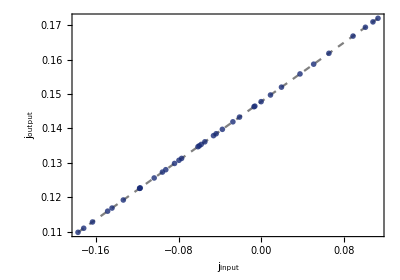

```mathematica
tab=SortBy[Flatten[Table[{jinput[R],joutput[R]},{x,0,5},{y,0,5}],1],First];
Show[Plot[λ0+λ1 ji/.values,{ji,tab[[1,1]],tab[[-1,1]]},PlotStyle->{Gray,Dashed}],ListPlot[tab,PlotMarkers->{{Graphics[{ColorData["BlueGreenYellow"][0.1],Disk[{0,0}]}],0.03}},PlotStyle->{{ColorData["BlueGreenYellow"][0.1],Opacity[0.8],Thickness[0.01]}}],ImageSize->400,AspectRatio->.7,Axes->False,Frame->True,FrameStyle->Black,LabelStyle->{FontFamily->"Times"},FrameLabel->{"j_input","j_output"}]
```

### Current bounds

As a spin-off result, we also showed that spanning tree polynomials bound the values a current can take under the perturbation of its rates. Here are the lower and upper bounds:

```mathematica
R={{0,r12,r13,r14},{r21,0,r23,r24},{r31,r32,0,r34},{r41,r42,r43,0}};
values={r12->x,r13->RandomReal[],r14->RandomReal[],r21->y,r23->RandomReal[],r24->RandomReal[],r31->RandomReal[],r32->RandomReal[],r34->RandomReal[],r41->RandomReal[],r42->RandomReal[],r43->RandomReal[]};
edge={1,2};
pss=SteadyState[R-DiagonalMatrix[Total[R]]];
jedge=pss[[edge[[1]]]] R[[edge[[2]],edge[[1]]]]-pss[[edge[[2]]]] R[[edge[[1]],edge[[2]]]];
```

```mathematica
trees=TreesFromRateMatrix[R];

rootedtrees=RootedTree[#,edge[[2]]]&/@trees;
nummin=Total@Table[(Times@@(R[[#2,#1]]&@@@({#[[1]],#[[2]]}&/@rt))),{rt,Deletion[rootedtrees,edge]}];
denmin=Tau[R][{edge},{Reverse@edge}];
min=-nummin/denmin;

rootedtrees=RootedTree[#,edge[[1]]]&/@trees;
nummax=Total@Table[(Times@@(R[[#2,#1]]&@@@({#[[1]],#[[2]]}&/@rt))),{rt,Deletion[rootedtrees,Reverse@edge]}];
denmax=Tau[R][{Reverse@edge},{edge}];
max=nummax/denmax;

{min,max}/.values
```

{-0.30293,0.129856}

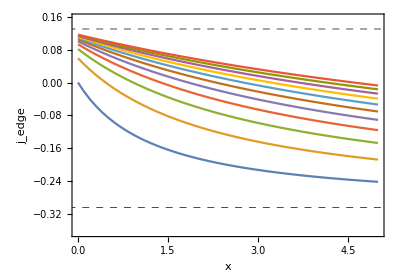

```mathematica
ListLinePlot[Evaluate@Table[{x,jedge/.values},{y,0,10},{x,0,5,.1}],GridLines->{{},{min/.values,max/.values}},GridLinesStyle->Directive[Dashed,Thick,Black],PlotRange->{Automatic,1.2{min/.values,max/.values}},Axes->False,Frame->True,FrameStyle->Black,ImageSize->400,AspectRatio->.7,LabelStyle->{FontFamily->"Times"},FrameLabel->{"x","j_edge"}]
```